Here we support some of the computations that appear in the manuscript (see README).

## 1. Introduction

```mathematica
Subscript[σB, 1][t_]:=Piecewise[{{-1/2,t<=-1/2},{t,t<=1/2}},1/2]
Subscript[σB, 2][t_]:=Piecewise[{{-1/2,t<=-1},{t(1-Abs[t]/2),t<=1}},1/2]
id[t_]:=t
```

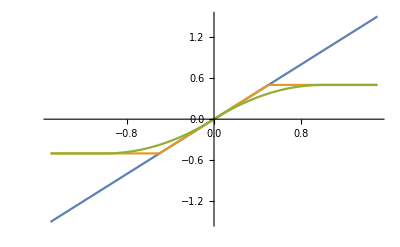

```mathematica
Plot[{t,Subscript[σB, 1][t],Subscript[σB, 2][t]},{t,-1.5,1.5}]
```

### Refinability

```mathematica
Subscript[σB, 1][t]==1/2 Subscript[σB, 1][2t+1/2]+1/2 Subscript[σB, 1][2t-1/2]//Simplify
Subscript[σB, 2][t]==1/4 Subscript[σB, 2][2t+1]+1/2 Subscript[σB, 2][2t]+1/4 Subscript[σB, 2][2t-1]//FullSimplify
A=2;τ=(A-1)/2;id[t]==Sum[1/(2A)id[2t+τ-l],{l,0,A-1}]//FullSimplify
```

True

True

True

### Figure 1

Refinability property of σB_1:

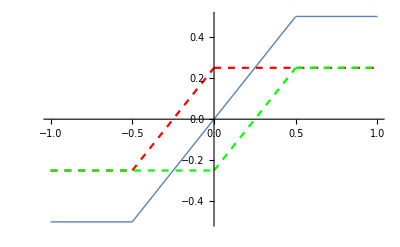

```mathematica
p1=Plot[Subscript[σB, 1][t],{t,-1,1},PlotStyle->Thick];
p2=Plot[1/2 Subscript[σB, 1][2t+1/2],{t,-1,1},PlotStyle->{Dashed,Red}];
p3=Plot[1/2 Subscript[σB, 1][2t-1/2],{t,-1,1},PlotStyle->{Dashed,Green}];
Show[p1,p2,p3]
```

Refinability property of σB_2:

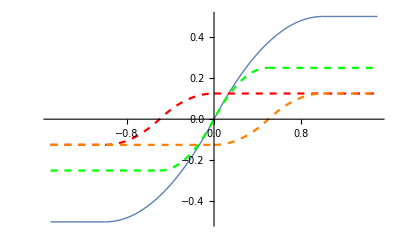

```mathematica
p1=Plot[Subscript[σB, 2][t],{t,-1.5,1.5},PlotStyle->Thick];
p2=Plot[{1/4 Subscript[σB, 2][2t+1]},{t,-1.5,1.5},PlotStyle->{Dashed,Red}];
p3=Plot[{1/2 Subscript[σB, 2][2t]},{t,-1.5,1.5},PlotStyle->{Dashed, Green}];
p4=Plot[{1/4 Subscript[σB, 2][2t-1]},{t,-1.5,1.5},PlotStyle->{Dashed,Orange}];
Show[p1,p2,p3,p4]
```

Refinability property of id:

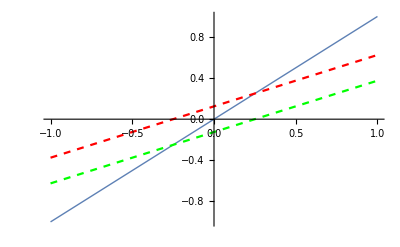

```mathematica
p1=Plot[id[t],{t,-1,1},PlotStyle->Thick];
p2=Plot[1/4id[2t+1/2],{t,-1,1},PlotStyle->{Dashed,Red}];
p3=Plot[1/4id[2t-1/2],{t,-1,1},PlotStyle->{Dashed,Green}];
Show[p1,p2,p3]
```

### Summing the identity

```mathematica
Assuming[-1/2<=t<=1/2,Subscript[σB, 1][t]==t//Simplify]
Assuming[-1/2<=t<=1/2,Subscript[σB, 2][t+1/2]+Subscript[σB, 2][t-1/2]==t//Simplify]
```

True

True

Visual verification:

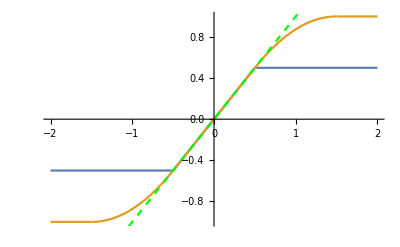

```mathematica
p1=Plot[{Subscript[σB, 1][t],Subscript[σB, 2][t+1/2]+Subscript[σB, 2][t-1/2]},{t,-2,2}];
p2 = Plot[t,{t,-2,2},PlotStyle->{Dashed,Green}];
Show[p1,p2]
```

## 3.1 B - Spline - based activation functions

### Explicit definition

```mathematica
ϕB[d_][t_]:=Sum[(-1)^l/(d!)Binomial[d+1,l]Max[t-l,0]^d,{l,0,d+1}]
```

### Definition by convolution

```mathematica
Φ0[t_]:=Piecewise[{{1,0<=t<1}},0]
ΦB[d_][t_]:=If[d>0&&d∈ Integers,Convolve[ΦB[d-1][tmp[d]],Φ0[tmp[d]],tmp[d],t],Φ0[t]]
```

```mathematica
ΦB[0][t]//FullSimplify
```

Piecewise[{{1, 0≤t<1}, {0, True}}]

```mathematica
ΦB[1][t]//FullSimplify
ΦB[1][t]==Max[0,1-Abs[t-1]]//FullSimplify
```

Piecewise[{{2-t, 1≤t<2}, {t, 0<t<1}, {0, True}}]

True

```mathematica
ΦB[2][t]//FullSimplify
```

Piecewise[{{t^2/2, 0<t≤1}, {-3/2-(-3+t) t, 1<t<2}, {1/2 (-3+t)^2, 2≤t<3}, {0, True}}]

```mathematica
ΦB[3][t]//FullSimplify
```

Piecewise[{{t^3/6, 0<t≤1}, {2/3-1/2 (-2+t)^2 t, 1<t≤2}, {-1/6 (-4+t)^3, 3≤t<4}, {-22/3+1/2 t (20+(-8+t) t), 2<t<3}, {0, True}}]

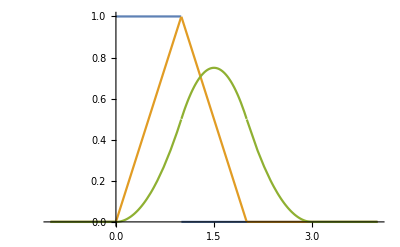

```mathematica
Plot[{ΦB[0][t],ΦB[1][t],ΦB[2][t]},{t,-1,4}]
```

Check that both definitions coincide:

```mathematica
Table[ΦB[d][t]-ϕB[d][t],{d,1,3}]//FullSimplify
```

{0,0,0}

### Refinability

```mathematica
Table[
ϕB[d][t]-Sum[2^(-d)Binomial[d+1,l]ϕB[d][2t-l],{l,0,d+1}]//FullSimplify,
{d,1,2}]
```

{0,0}

### Sum

```mathematica
d=1;n=10;
Assuming[-n+1≤t≤n+1,1==Sum[ϕB[d][t-i],{i,-n,n}]//FullSimplify]
Assuming[-n+1≤t≤n+1,t-(d+1)/2==Sum[i ΦB[d][t-i],{i,-n,n}]//FullSimplify]
```

True

True

```mathematica
d=2;n=10;
Assuming[-n+2≤t≤n+1,1==Sum[ΦB[d][t-i],{i,-n,n}]//FullSimplify]
Assuming[-n+2≤t≤n+1,t-(d+1)/2==Sum[i ΦB[d][t-i],{i,-n,n}]//FullSimplify]
```

True

True

Visual verification :

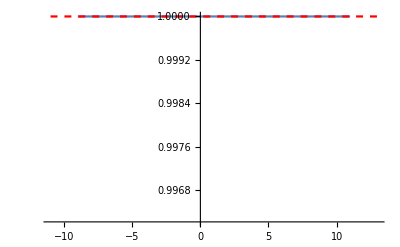

```mathematica
n=10;
p1=Plot[Sum[ϕB[1][t-i],{i,-n,n}],{t,-n-1,n+3}];
p2=Plot[1,{t,-n-1,n+3},PlotStyle->{Dashed,Red}];
Show[p1,p2]
```

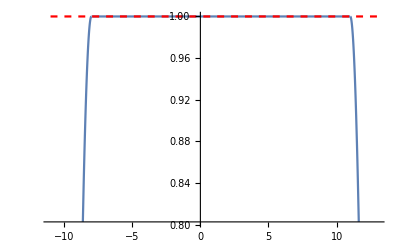

```mathematica
n=10;
p1=Plot[Sum[ϕB[2][t-i],{i,-n,n}],{t,-n-1,n+3}];
p2=Plot[1,{t,-n-1,n+3},PlotStyle->{Dashed,Red}];
Show[p1,p2]
```

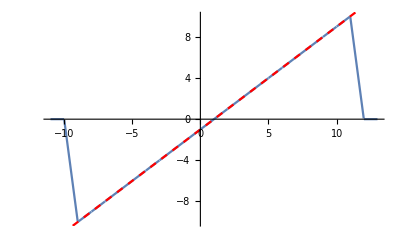

```mathematica
d=1;n=10;
p1=Plot[Sum[i ϕB[d][t-i],{i,-n,n}],{t,-n-1,n+3}];
p2=Plot[t-(d+1)/2,{t,-n-1,n+3},PlotStyle->{Dashed,Red}];
Show[p1,p2]
```

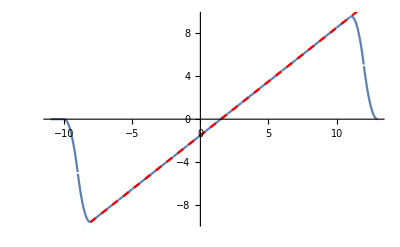

```mathematica
d=2;n=10;
p1=Plot[Sum[i ϕB[d][t-i],{i,-n,n}],{t,-n-1,n+3}];
p2=Plot[t-(d+1)/2,{t,-n-1,n+3},PlotStyle->{Dashed,Red}];
Show[p1,p2]
```

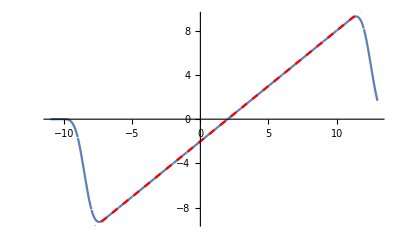

```mathematica
d=3;n=10;
p1=Plot[Sum[i ϕB[d][t-i],{i,-n,n}],{t,-n-1,n+3}];
p2=Plot[t-(d+1)/2,{t,-n-1,n+3},PlotStyle->{Dashed,Red}];
Show[p1,p2]
```

### Theorem 10

#### (a)

```mathematica
σB[d_][t_]:=Piecewise[{{-1/2,t<=-d/2},{-1/2+Sum[ϕB[d][t+d/2-m],{m,0,d-1}],t<d/2}},1/2]
```

```mathematica
d=1;Subscript[σB, 1][t]==σB[d][t]//FullSimplify
d=2;Subscript[σB, 2][t]==σB[d][t]//FullSimplify
```

True

True

#### (c)

```mathematica
Table[
σB[d][t]==Sum[ 2^-d Binomial[d,l]σB[d][2t+d/2-l],{l,0,d}]//FullSimplify,
{d,1,3}]
```

{True,True,True}

#### (d)

```mathematica
Table[Assuming[-(B-d+1)/2<=t<=(B-d+1)/2,t==Sum[σB[d][t+(B-1)/2-l],{l,0,B-1}]//FullSimplify],
{B,d,d+2},
{d,1,3}]
```

{{True,True,True},{True,True,True},{True,True,True}}

#### (e)

```mathematica
Table[σB[d][t]-(-1/2+1/(d!)Sum[(-1)^l Binomial[d,l] Max[t+d/2-l,0]^d,{l,0,d}])//FullSimplify,
{d,1,3}]
```

{0,0,0}

#### (f)

```mathematica
Assuming[t∈Reals,Table[
σB[d+1][t]==Integrate[σB[d][s],{s,t-1/2,t+1/2}]//FullSimplify,
{d,1,3}]]
```

{True,True,True}

### (g)

```mathematica
Assuming[t∈Reals,Table[
σB[d]'[t]==ΦB[d-1][t+d/2]//FullSimplify,
{d,1,3}]]
```

{t<-1/2||-1/2<t<1/2||2 t>1,True,True}

### Proposition 11

```mathematica
Assuming[-1/2<σB[1][t]<1/2//FullSimplify,σB[1]'[t]==1//FullSimplify]
```

True

```mathematica
Assuming[-1/2<σB[2][t]<=0//FullSimplify,σB[2]'[t]==√(1+2σB[2][t])//FullSimplify]
```

True

```mathematica
Assuming[0<σB[2][t]<1/2//FullSimplify,σB[2]'[t]==√(1-2σB[2][t])//FullSimplify]
```

True

#### Assistance for the proof of the case d=2

If t ∈ (-1,0], then z = t(1+t/2) ∈ (-1/2,0]:

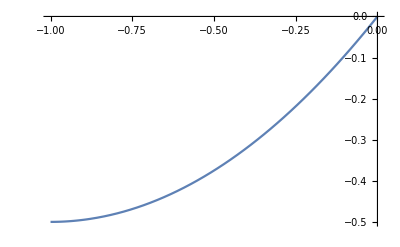

```mathematica
Plot[t(1+t/2),{t,-1,0}]
```

```mathematica
Solve[z==t(1+t/2),t]
```

{{t→-1-√(1+2 z)},{t→-1+√(1+2 z)}}

For z ∈ (-1/2,0], t = -1 + √(1 + 2z) ∈ (-1,0]:

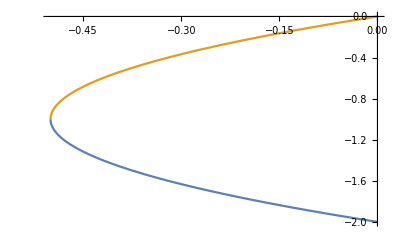

```mathematica
Plot[{-1-√(1+2 z),-1+√(1+2 z)},{z,-1/2,0}]
```

If t ∈ (0,1), then z = t (1 - t/2) ∈ (0,1/2):

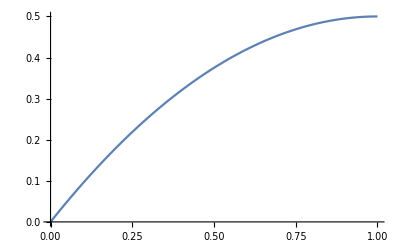

```mathematica
Plot[t(1-t/2),{t,0,1}]
```

```mathematica
Solve[z==t(1-t/2),t]
```

{{t→1-√(1-2 z)},{t→1+√(1-2 z)}}

For z ∈ (0,1/2), t = 1 - √(1 - 2z) ∈ (0,1):

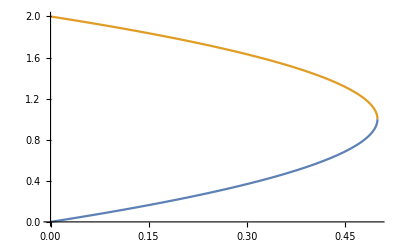

```mathematica
Plot[{1-√(1-2 z),1+√(1-2 z)},{z,0,1/2}]
```

### Theorem 13

#### (c)

```mathematica
Table[
σB[d][t]-σB[d][t-1]==ΦB[d][t+d/2]//FullSimplify,
{d,1,3}]
```

{True,True,True}

#### (d)

```mathematica
Assuming[t∈Reals,
Table[ϕB[d][t]==ϕB[d][d+1-t]//FullSimplify,
{d,1,3}]]
```

{True,True,True}

```mathematica
Assuming[t∈Reals,
Table[-σB[d][t]==σB[d][-t]//FullSimplify,
{d,1,3}]]
```

{True,True,True}